```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

### Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,len_]:=Module[{temp=Range[1,len],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];Print[ii];,{ii,len}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tmuscan/results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])(const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tmuscan/results/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/Tmuscan/results/"<>ToString[res]<>".dat"];
```

## Critical Temperature 155MeV

```mathematica
Tmuscan=Join[Table[{0.155,i},{i,0.,0.155,0.005}],Table[{0.155,i},{i,0.16,1.,0.05}]]
```

{{0.155,0.},{0.155,0.005},{0.155,0.01},{0.155,0.015},{0.155,0.02},{0.155,0.025},{0.155,0.03},{0.155,0.035},{0.155,0.04},{0.155,0.045},{0.155,0.05},{0.155,0.055},{0.155,0.06},{0.155,0.065},{0.155,0.07},{0.155,0.075},{0.155,0.08},{0.155,0.085},{0.155,0.09},{0.155,0.095},{0.155,0.1},{0.155,0.105},{0.155,0.11},{0.155,0.115},{0.155,0.12},{0.155,0.125},{0.155,0.13},{0.155,0.135},{0.155,0.14},{0.155,0.145},{0.155,0.15},{0.155,0.155},{0.155,0.16},{0.155,0.21},{0.155,0.26},{0.155,0.31},{0.155,0.36},{0.155,0.41},{0.155,0.46},{0.155,0.51},{0.155,0.56},{0.155,0.61},{0.155,0.66},{0.155,0.71},{0.155,0.76},{0.155,0.81},{0.155,0.86},{0.155,0.91},{0.155,0.96}}

```mathematica
Do[ccdataTc[n]=Import["spectraldata/Tmuscan/cc/swccT"<>ToString[Round[1000 Tmuscan[[n,1]]]]<>"mu"<>ToString[Round[1000 Tmuscan[[n,2]]]]<>"spectra.dat"];,{n,Length[Tmuscan]}];
Do[ccdataTcu[n]=Import["spectraldata/Tmuscan/cc/swccT"<>ToString[Round[1000 Tmuscan[[n,1]]]]<>"mu"<>ToString[Round [1000 Tmuscan[[n,2]]]]<>"uspectra.dat"];,{n,Length[Tmuscan]}];
Do[ccdataTcl[n]=Import["spectraldata/Tmuscan/cc/swccT"<>ToString[Round[1000 Tmuscan[[n,1]]]]<>"mu"<>ToString[Round[1000 Tmuscan[[n,2]]]]<>"lspectra.dat"];,{n,Length[Tmuscan]}];
```

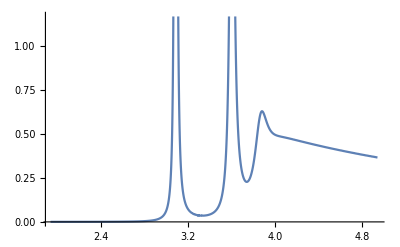

```mathematica
ListPlot[ccdataTcl[6],Joined->True]
```

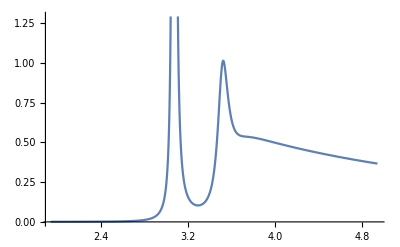

```mathematica
ListPlot[ccdataTc[6],Joined->True]
```

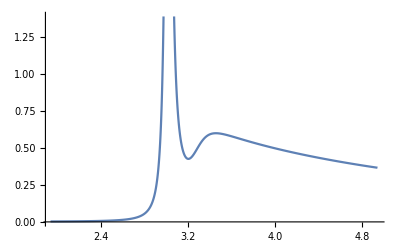

```mathematica
ListPlot[ccdataTcu[6],Joined->True]
```

### Perform Fitting

```mathematica
Clear[ccmodelTc,ccmodelTcl,ccmodelTcu]
fitnew[ccdataTc,ccmodelTc,Length[Tmuscan]];
fitnew[ccdataTcu,ccmodelTcu,Length[Tmuscan]];
fitnew[ccdataTcl,ccmodelTcl,Length[Tmuscan]];
```

```mathematica
Do[If[Length[ccmodelTc[[i]]]>2,ccmodelTc[[i]]=ccmodelTc[[i,;;2]]];,{i,Length[ccmodelTc]}];
Do[If[Length[ccmodelTcu[[i]]]>2,ccmodelTcu[[i]]=ccmodelTcu[[i,;;2]]];,{i,Length[ccmodelTcu]}];
Do[If[Length[ccmodelTcl[[i]]]>2,ccmodelTcl[[i]]=ccmodelTcl[[i,;;2]]];,{i,Length[ccmodelTcl]}];
```

```mathematica
Clear[Tcwrfitcc,Tcgfitcc,Tcareafitcc,Tccfitcc,Tcdfitcc,Tcsfitcc,Tcs2fitcc,Tcwrfitccu,Tcgfitccu,Tcareafitccu,Tccfitccu,Tcdfitccu,Tcsfitccu,Tcs2fitccu,Tcwrfitccl,Tcgfitccl,Tcareafitccl,Tccfitccl,Tcdfitccl,Tcsfitccl,Tcs2fitccl];
store[wr,Tcwrfitcc,ccmodelTc];
store[Γ,Tcgfitcc,ccmodelTc];
store[const,Tccfitcc,ccmodelTc];
store[δbg,Tcdfitcc,ccmodelTc];
store[shift,Tcsfitcc,ccmodelTc];
store[shift2,Tcs2fitcc,ccmodelTc];
storearea[Tcareafitcc,ccmodelTc];
store[wr,Tcwrfitccu,ccmodelTcu];
store[Γ,Tcgfitccu,ccmodelTcu];
store[const,Tccfitccu,ccmodelTcu];
store[δbg,Tcdfitccu,ccmodelTcu];
store[shift,Tcsfitccu,ccmodelTcu];
store[shift2,Tcs2fitccu,ccmodelTcu];
storearea[Tcareafitccu,ccmodelTcu];
store[wr,Tcwrfitccl,ccmodelTcl];
store[Γ,Tcgfitccl,ccmodelTcl];
store[const,Tccfitccl,ccmodelTcl];
store[δbg,Tcdfitccl,ccmodelTcl];
store[shift,Tcsfitccl,ccmodelTcl];
store[shift2,Tcs2fitccl,ccmodelTcl];
storearea[Tcareafitccl,ccmodelTcl];
```

### Import previous results

```mathematica
import[Tcwrfitcc];
import[Tcgfitcc];
import[Tccfitcc];
import[Tcdfitcc];
import[Tcsfitcc];
import[Tcs2fitcc];
import[Tcareafitcc];
import[Tcwrfitccu];
import[Tcgfitccu];
import[Tccfitccu];
import[Tcdfitccu];
import[Tcsfitccu];
import[Tcs2fitccu];
import[Tcareafitccu];
import[Tcwrfitccl];
import[Tcgfitccl];
import[Tccfitccl];
import[Tcdfitccl];
import[Tcsfitccl];
import[Tcs2fitccl];
import[Tcareafitccl];
```

Import::nffil: File not found during Import.

Set::shape: Lists {{3.07185,3.5111},{3.07185,3.51106},{3.07182,3.51089},{3.07178,3.51065},{3.07172,3.51031},{3.07165,3.50985},{3.07156,3.5093},{3.07146,3.50862},{3.07134,3.50787},{3.0712,3.50705},«29»,{3.02968,3.31459},{3.02554,3.30537},{3.02156,3.29704},{3.01772,3.2897},{3.014,3.28316},{3.01038,3.27747},{3.00682,3.27231},{3.00332,3.26794},{2.99986,3.26437},{2.99641,3.26169}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0180943,0.107211},{0.0180981,0.107295},{0.0181135,0.107381},{0.0181717,0.107616},{0.0182158,0.107921},{0.018169,0.108176},{0.0181447,0.108538},{0.0183902,0.109178},{0.018464,0.109769},«31»,{0.0513198,0.319993},{0.0540795,0.335187},{0.0566345,0.347985},{0.0591406,0.361252},{0.0615336,0.37043},{0.0639054,0.381597},{0.0662011,0.390615},{0.0684442,0.39747},{0.0707008,0.403352}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{18.2399,0.738781},{18.2356,0.738566},{18.219,0.736897},{18.1584,0.73443},{18.1117,0.731289},{18.1549,0.727668},{18.1746,0.723037},{17.9269,0.715516},{17.8493,0.708863},{17.8732,0.702479},«30»,{5.6705,4.89624×10^-6},{5.32059,6.13789×10^-6},{5.02483,7.95696×10^-6},{4.75988,9.97645×10^-6},{4.52575,0.0000138693},{4.31166,0.0000183236},{4.11758,0.0000249411},{3.93968,0.0000348819},{3.77231,0.0000480416}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.515601,0.285994},{0.515677,0.285752},{0.515617,0.286496},{0.514854,0.286943},{0.514786,0.287495},{0.518291,0.288945},{0.521284,0.290457},{0.515552,0.292179},{0.5163,0.294},{0.520754,0.295779},«30»,{0.527968,0.256505},{0.528701,0.237473},{0.530339,0.218941},{0.531252,0.202184},{0.532418,0.184534},{0.533299,0.16909},{0.533929,0.153626},{0.534677,0.138221},{0.535032,0.123354}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0571109,0.814419},{0.0575065,0.814963},{0.0590224,0.812933},{0.0585385,0.811317},{0.057612,0.809623},{0.0570259,0.806498},{0.0581641,0.803172},{0.058683,0.796301},{0.0592047,0.791003},{0.059027,0.786946},«30»,{0.308565,-0.025642},{0.341925,-0.0370104},{0.375914,-0.047112},{0.409756,-0.0592826},{0.443329,-0.0675312},{0.475801,-0.0786241},{0.510416,-0.0882893},{0.544617,-0.0968441},{0.578331,-0.105566}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0177549,0.249899},{0.0177526,0.249743},{0.0177535,0.250111},{0.0178366,0.25039},{0.0178723,0.250714},{0.0178902,0.25127},{0.0179534,0.251927},{0.0180869,0.253101},{0.0182055,0.253985},{0.0182679,0.25466},«30»,{0.0735616,0.480233},{0.0803111,0.489707},{0.0869853,0.499431},{0.0938046,0.50924},{0.100713,0.519079},{0.107598,0.528747},{0.114779,0.538347},{0.12211,0.547835},{0.129615,0.557188}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.518421,0.124415},{0.518411,0.124477},{0.518378,0.124296},{0.518316,0.12415},{0.518237,0.123969},{0.518135,0.123647},{0.518006,0.123272},{0.51786,0.122708},{0.517687,0.122226},«31»,{0.457116,2.46107×10^-6},{0.451973,3.23166×10^-6},{0.447015,4.34938×10^-6},{0.442183,5.66116×10^-6},{0.437445,8.0701×10^-6},{0.432815,0.0000109834},{0.428181,0.0000153033},{0.423562,0.0000217783},{0.41894,0.0000304384}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{3.01735,3.28891},{3.01734,3.28883},{3.01731,3.28881},{3.01727,3.28879},{3.0172,3.28875},{3.01712,3.28843},{3.01702,3.28839},{3.0169,3.28815},{3.01676,3.28783},{3.01661,3.28772},{3.01644,3.28729},{3.01625,3.28719},«26»,{2.98119,3.25994},{2.97754,3.26207},{2.97408,3.2678},{2.97075,3.41708},{2.96755},{2.96442},{2.96135},{2.95831},{2.95528},{2.95225},{2.94918}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0568801,0.350476},{0.0568896,0.351182},{0.0569022,0.34996},{0.0569337,0.350213},{0.0569877,0.350297},{0.0570397,0.351349},{0.0571542,0.351973},{0.0571892,0.352134},{0.0572964,0.352168},{0.0574144,0.35224},{0.0575704,0.353232},«27»,{0.0803095,0.396349},{0.0825524,0.383004},{0.0846794,0.35612},{0.0867621,1.17683},{0.0885346},{0.0905875},{0.0924375},{0.094287},{0.0960948},{0.0979258},{0.0997631}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{4.99754,8.01928×10^-6},{4.99691,7.92697×10^-6},{4.99473,8.33147×10^-6},{4.99132,8.17547×10^-6},{4.98635,8.07798×10^-6},{4.98031,8.2452×10^-6},{4.96854,7.94623×10^-6},{4.96419,8.10793×10^-6},{4.95299,8.50347×10^-6},{4.94065,8.35638×10^-6},{4.92415,8.67144×10^-6},«27»,{3.15877,0.000353193},{3.03588,0.000822229},{2.9247,0.00248124},{2.82264,0.384365},{2.73638},{2.64578},{2.56604},{2.49067},{2.41839},{2.34954},{2.28278}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.530356,0.218018},{0.530668,0.218413},{0.530019,0.217453},{0.530013,0.217275},{0.53061,0.216865},{0.530463,0.217009},{0.529549,0.216563},{0.530548,0.215961},{0.530394,0.215049},{0.530387,0.21398},{0.529391,0.21338},«27»,{0.539525,0.0617792},{0.541766,0.0483631},{0.543253,0.0343271},{0.54545,0.314008},{0.549218},{0.551368},{0.554075},{0.557434},{0.56081},{0.563867},{0.5681}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.379872,-0.0495219},{0.377903,-0.0502831},{0.382384,-0.0485203},{0.382976,-0.0490767},{0.379696,-0.0494517},{0.381384,-0.0500841},{0.384857,-0.0513555},{0.382814,-0.0511858},{0.384588,-0.0506897},{0.385204,-0.0512405},{0.390187,-0.0517338},«27»,{0.714387,-0.129487},{0.74018,-0.129221},{0.765888,-0.12041},{0.784646,-0.706214},{0.801975},{0.813986},{0.827222},{0.836446},{0.844935},{0.853405},{0.856606}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0877342,0.500275},{0.0876055,0.500238},{0.0879421,0.500331},{0.0880175,0.500518},{0.0878409,0.500783},{0.0881195,0.500813},{0.0884661,0.50127},{0.0884774,0.501492},{0.088718,0.501794},{0.0889805,0.502386},{0.0895925,0.502728},«27»,{0.163413,0.593418},{0.171275,0.599985},{0.179037,0.604481},{0.186148,0.220104},{0.192759},{0.199443},{0.205635},{0.211343},{0.217424},{0.222919},{0.228489}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.446515,4.41482×10^-6},{0.446534,4.3728×10^-6},{0.446438,4.57995×10^-6},{0.44638,4.49743×10^-6},{0.446359,4.44487×10^-6},{0.446224,4.55051×10^-6},{0.446064,4.39329×10^-6},{0.445947,4.48474×10^-6},{0.445774,4.70399×10^-6},{0.445579,4.62356×10^-6},{0.445298,4.8114×10^-6},«28»,{0.393671,0.00049467},{0.389026,0.00138798},{0.384685,0.710522},{0.380548},{0.376479},{0.372591},{0.368882},{0.365045},{0.36141},{0.357728}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{3.08671,3.60304},{3.08671,3.603},{3.08669,3.6029},{3.08667,3.60272},{3.08663,3.60248},{3.08658,3.60217},{3.08652,3.60178},{3.08646,3.60133},{3.08638,3.60081},{3.08629,3.60022},«29»,{3.05535,3.41733},{3.05188,3.3996},{3.0485,3.3825},{3.04518,3.36605},{3.04192,3.35024},{3.0387,3.33668},{3.03552,3.32855},{3.03235,3.32082},{3.02919,3.31342},{3.02603,3.3064}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.00693915,0.0420771},{0.00693427,0.0420987},{0.00692792,0.0421493},{0.00698752,0.0423111},{0.00696766,0.042438},{0.00703759,0.0426789},{0.00707595,0.042937},{0.0071701,0.0432855},{0.00722933,0.0436388},«31»,{0.03281,0.218075},{0.0351781,0.233805},{0.0376107,0.247576},{0.0399193,0.259177},{0.042195,0.269676},{0.0444156,0.281652},{0.0465191,0.293742},{0.0488189,0.306255},{0.0509787,0.318518}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{49.582,3.17617},{49.6157,3.17414},{49.6589,3.16892},{49.2317,3.15477},{49.3666,3.14254},{48.8689,3.12121},{48.5965,3.09788},{47.949,3.06784},{47.5449,3.03693},{47.1773,3.00333},«30»,{9.53156,0.165604},{8.80939,0.115228},{8.16612,0.0696313},{7.62649,0.0282959},{7.15235,0.0000361934},{6.73579,7.30074×10^-6},{6.37552,4.65072×10^-6},{6.02225,4.30519×10^-6},{5.7162,4.75202×10^-6}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.524857,0.216055},{0.526585,0.216143},{0.529213,0.216143},{0.523895,0.215877},{0.527896,0.216303},{0.525441,0.216321},{0.525589,0.216426},{0.522278,0.216514},{0.522623,0.216392},{0.521067,0.216767},«30»,{0.517356,0.368275},{0.519864,0.363836},{0.519916,0.356053},{0.521517,0.345},{0.522583,0.329396},{0.523965,0.309591},{0.526631,0.291809},{0.526541,0.275017},{0.527691,0.259248}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0288028,0.218709},{0.0171807,0.21889},{0.00427128,0.220709},{0.0188089,0.22144},{0.0331231,0.22284},{0.011742,0.225035},{0.0300592,0.228668},{0.00840829,0.231125},{0.0111094,0.236358},«31»,{0.138583,0.214678},{0.155512,0.147116},{0.174969,0.0862587},{0.192612,0.032779},{0.213522,-0.00283863},{0.235391,-0.00456446},{0.257119,-0.00933126},{0.279965,-0.0164777},{0.305319,-0.0248804}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.00607448,0.0492074},{0.0062158,0.0492453},{0.00623251,0.049449},{0.0062807,0.0496895},{0.00633802,0.0499522},{0.00643065,0.0503596},{0.00633868,0.0509326},{0.00636602,0.0515406},{0.00648198,0.052273},«31»,{0.0375808,0.360785},{0.0414517,0.383722},{0.0455836,0.408186},{0.0496589,0.433448},{0.0539749,0.453825},{0.0584368,0.459355},{0.0629412,0.465358},{0.0677739,0.471999},{0.0728198,0.47905}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.540443,0.209927},{0.54043,0.209901},{0.540406,0.209807},{0.540366,0.209673},{0.540307,0.209486},{0.540227,0.209246},{0.540144,0.208938},{0.540039,0.208591},{0.539911,0.208174},«31»,{0.491237,0.0567279},{0.486786,0.0423185},{0.482445,0.0270791},{0.47822,0.0115197},{0.474056,0.0000153317},{0.469942,3.22998×10^-6},{0.465872,2.14588×10^-6},{0.461814,2.07107×10^-6},{0.457737,2.37757×10^-6}} and $Failed are not the same shape.

### View results

```mathematica
Manipulate[Show[{ListPlot[ccdataTc[i],Joined->True],Plot[BW[x,Tcwrfitcc[[i,ii]],Tcgfitcc[[i,ii]],Tcdfitcc[[i,ii]],Tccfitcc[[i,ii]],Tcsfitcc[[i,ii]],Tcs2fitcc[[i,ii]]],{x,0.7Tcwrfitcc[[i,ii]],1.3Tcwrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,Tcwrfitcc[[i,ii]],Tcgfitcc[[i,ii]],Tccfitcc[[i,ii]]],{x,0.7Tcwrfitcc[[i,ii]],1.3Tcwrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[Tcwrfitcc],1},{ii,1,Length[Tcwrfitcc[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdataTcu[i],Joined->True],Plot[BW[x,Tcwrfitccu[[i,ii]],Tcgfitccu[[i,ii]],Tcdfitccu[[i,ii]],Tccfitccu[[i,ii]],Tcsfitccu[[i,ii]],Tcs2fitccu[[i,ii]]],{x,0.7Tcwrfitccu[[i,ii]],1.3Tcwrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,Tcwrfitccu[[i,ii]],Tcgfitccu[[i,ii]],Tccfitccu[[i,ii]]],{x,0.7Tcwrfitccu[[i,ii]],1.3Tcwrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[Tcwrfitccu],1},{ii,1,Length[Tcwrfitccu[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdataTcl[i],Joined->True],Plot[BW[x,Tcwrfitccl[[i,ii]],Tcgfitccl[[i,ii]],Tcdfitccl[[i,ii]],Tccfitccl[[i,ii]],Tcsfitccl[[i,ii]],Tcs2fitccl[[i,ii]]],{x,0.7Tcwrfitccl[[i,ii]],1.3Tcwrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,Tcwrfitccl[[i,ii]],Tcgfitccl[[i,ii]],Tccfitccl[[i,ii]]],{x,0.7Tcwrfitccl[[i,ii]],1.3Tcwrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[Tcwrfitccl],1},{ii,1,Length[Tcwrfitccl[[1]]],1}]
```

### Dilepton ratio

```mathematica
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0Tc=ConstantArray[0,Length[Tcwrfitcc]];
Do[If[Length[Tcwrfitcc[[ii]]]==2,R0Tc[[ii]]={Tmuscan[[ii,2]],Emfactor (Tcareafitcc[[ii,2]]nB[Tcwrfitcc[[ii,2]],Tmuscan[[ii,1]]])/(Tcareafitcc[[ii,1]]nB[Tcwrfitcc[[ii,1]],Tmuscan[[ii,1]]])}],{ii,Length[R0Tc]}];
R0Tcu=ConstantArray[0,Length[Tcwrfitccu]];
Do[If[Length[Tcwrfitccu[[ii]]]==2,R0Tcu[[ii]]={Tmuscan[[ii,2]],Emfactor (Tcareafitccu[[ii,2]]nB[Tcwrfitccu[[ii,2]],Tmuscan[[ii,1]]])/(Tcareafitccu[[ii,1]]nB[Tcwrfitccu[[ii,1]],Tmuscan[[ii,1]]])}],{ii,Length[R0Tcu]}];
R0Tcl=ConstantArray[0,Length[Tcwrfitccl]];
Do[If[Length[Tcwrfitccl[[ii]]]==2,R0Tcl[[ii]]={Tmuscan[[ii,2]],Emfactor (Tcareafitccl[[ii,2]]nB[Tcwrfitccl[[ii,2]],Tmuscan[[ii,1]]])/(Tcareafitccl[[ii,1]]nB[Tcwrfitccl[[ii,1]],Tmuscan[[ii,1]]])}],{ii,Length[R0Tcl]}];
```

```mathematica
R0Tc=DeleteCases[R0Tc,0];
R0Tcu=DeleteCases[R0Tcu,0];
R0Tcl=DeleteCases[R0Tcl,0];
```

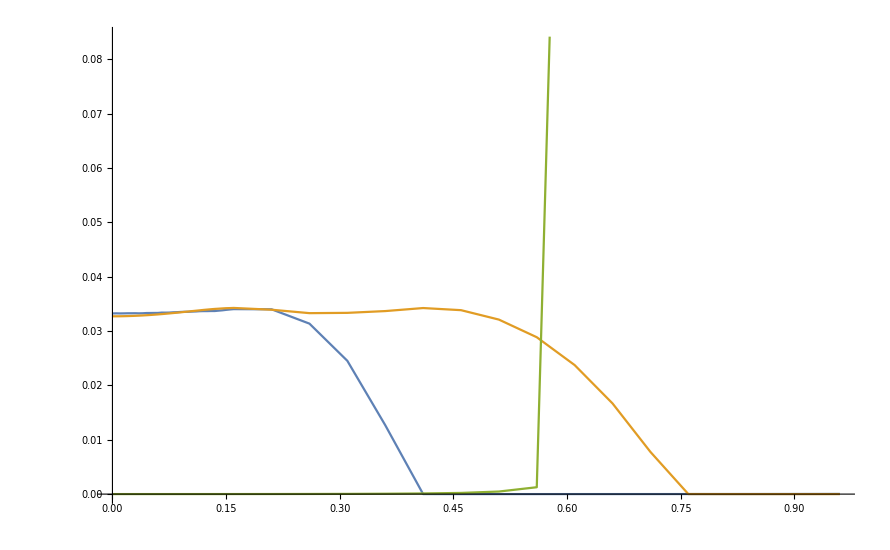

```mathematica
ListLinePlot[{R0Tc,R0Tcl,R0Tcu}]
```